```mathematica
NumberOfFlips:=1000
Goal := 1000000000
```

The factor the account is multiplied by for a given number of heads that occur in the trial, and a given value of f is defined by AccountFactor.  Since the starting value of the account is £1, this factor is equivalent to the final account value.

```mathematica
AccountFactor[heads_,f_]:=(1+2f)^(heads)*(1-f)^(NumberOfFlips-heads)
```

```mathematica
Plot3D[{Log[AccountFactor[heads,f]]}, {heads, 0, NumberOfFlips}, {f,0,1}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
AtGoal[heads_, f_] := AccountFactor[heads,f]≥Goal
```

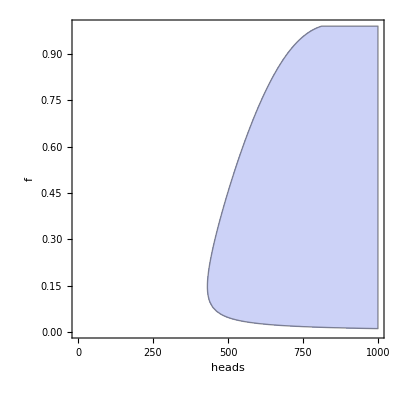

```mathematica
RegionPlot[AtGoal[heads,f],{heads,0,NumberOfFlips},{f,0,0.99},FrameLabel->Automatic]
```

Solve for the boundary of the region, optimal f value is the point with minimal number of heads to reach £1 billion.

```mathematica
curve = First[Solve[AccountFactor[heads,f]==Goal,heads]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{heads→-Log[1000000000/(1-f)^1000]/(Log[1-f]-Log[1+2 f])}

```mathematica
CurveExpr[f_] := heads/.curve
```

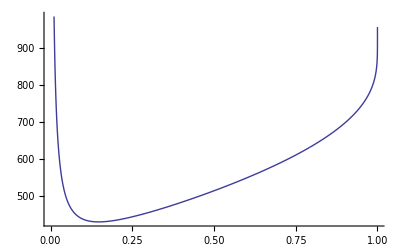

```mathematica
Plot[CurveExpr[f],{f,0,1},PlotPoints->10000]
```

```mathematica
root =FindRoot[D[CurveExpr[f],f]==0,{f,0.2}]
```

{f→0.146884}

```mathematica
min = CurveExpr[f]/.root
```

431.256

```mathematica
MinHeads = Ceiling[min]
```

432

Probability of becoming a billionaire is the likelihood of getting at least 432 heads.  This is a simple combinations problem.

```mathematica
p =Sum[(Factorial[NumberOfFlips]/(Factorial[h]*Factorial[NumberOfFlips-h]))/2^NumberOfFlips,{h,MinHeads,NumberOfFlips}]
```

1339376163873338327872103842943081186987026790532442387366533006134047414314050904009229201208540156620512861900943361481224568589232184931448651539303467066428253034773341495533577495717695880279594447344931930956440865348645230533665984291472954114962659293135811376099352289506470874380496075511631/1339385758982834151185531311325002263201756014631917009304687985462938813906170153116497973519619822659493341146941433531483931607115392554498072196837321850491820971853028873177634325632796392734744272769130809372947742658424845944895692993259632864321399559710817770957553728956578048354650708508672

```mathematica
N[p,12]
```

0.999992836187